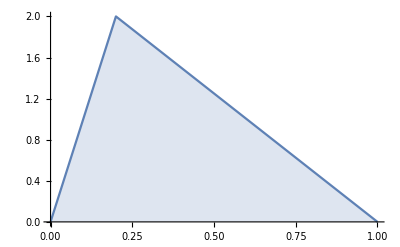

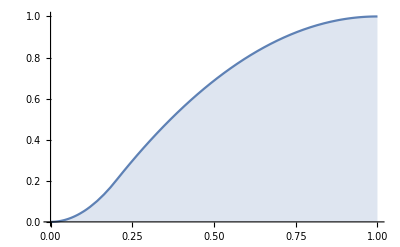

```mathematica
fpdf [x_]:=PDF[TriangularDistribution[{0,1},0.2],x];
fcdf[x_]:=CDF[TriangularDistribution[{0,1},0.2],x]
fcdfi[ξ_]:=InverseFunction[fcdf][ξ]
Plot[fpdf[x],{x,0,1},Filling->Axis,Exclusions->None]
Plot[fcdf[x],{x,0,1},Filling->Axis,Exclusions->None]
```

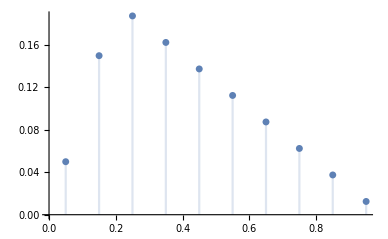

```mathematica
DiscretePlot[Integrate[fpdf[x],{x,y-0.05,y+0.05}],{y,0.05,0.95,0.1},Filling->Axis]
```

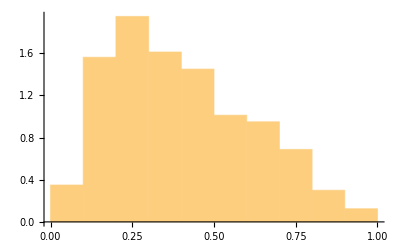

```mathematica
ξarray=RandomReal[1,{800}];
Parallelize[cyres=fcdfi[#]&/@ξarray];
Histogram[cyres,10,"PDF"]
```

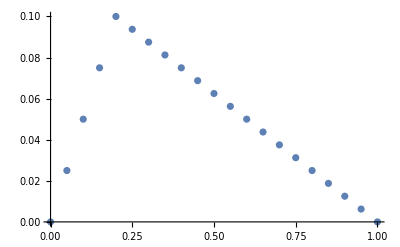

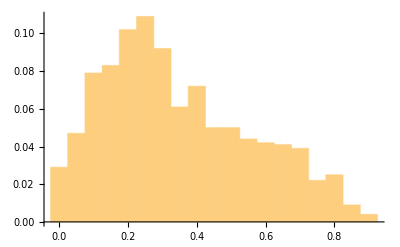

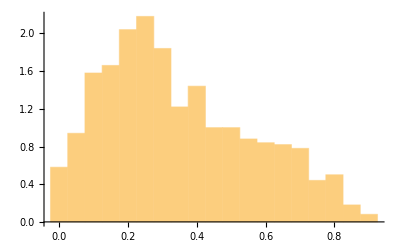

```mathematica
temp1 = fpdf[#]&/@Range[0,1,0.05];
lsp = temp1/Total[temp1];
ListPlot[Transpose[{Range[0,1,0.05],lsp}]]
lsy = Sum[lsp[[n]],{n,1,#}]&/@Range[2,Length[lsp]];
calk[ξ_]:=Position[ξ<#&/@lsy,True][[1,1]]
lsξarray=RandomReal[1,{1000}];
Parallelize[xkarray=Range[0,1,0.05][[calk[#]]]&/@lsξarray;]
Histogram[xkarray,21,"Probability"]
Histogram[xkarray,21,"PDF"]
```

-Graphics-

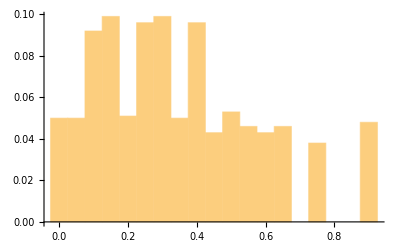

```mathematica
temp1 = fpdf[#]&/@Range[0,1,0.05];
lsp = temp1/Total[temp1];
ListPlot[Transpose[{Range[0,1,0.05],lsp}]]
lsy = Sum[lsp[[n]],{n,1,#}]&/@Range[2,Length[lsp]];
calk[ξ_]:=Position[ξ<=#&/@lsy,True][[1,1]]
lsξarray=RandomInteger[{0,20},{1000}]*0.05;
Parallelize[xkarray=Range[0,1,0.05][[calk[#]]]&/@lsξarray;]
Histogram[xkarray,21,"Probability"]
```

效果很差，写的有问题？

0.4825

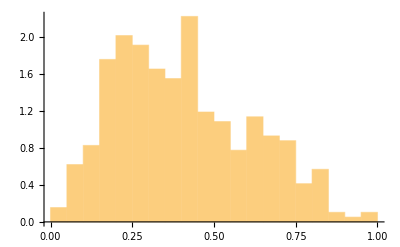

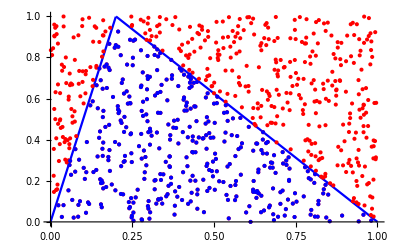

```mathematica
M=2;
ξarray=RandomReal[1,{800,2}];
sample =DeleteCases[If[M*ξarray[[#,2]]<fpdf[ξarray[[#,1]]],ξarray[[#]],Null;]&/@Range[Length[ξarray]],
Null];
N[Length[sample]/800]
Histogram[sample[[;;,1]],21,"PDF"]
Show[
{
Plot[fpdf[x]/M,{x,0,1},PlotStyle->{Blue}],
ListPlot[ξarray,PlotStyle->{Red}],
ListPlot[sample,PlotStyle->{Blue}]
}
]
```

InverseFunction::ifun: 反函数正在使用中. 对于多值反函数，有些值可能丢失.

1+√2 InverseErf[-1+2 temp]

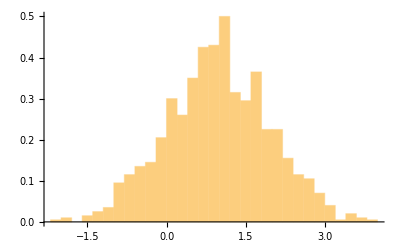

```mathematica
f[x_]:=1/(√(2*π))*Exp[(-(x-1)^2)/2]
f2[x_]:=Integrate[f[x1],{x1,-∞,x}]
t1 = InverseFunction[f2][temp]
if2[ξ_]:=t1/.temp-> ξ
Histogram[if2[#]&/@RandomReal[{0,1},{1000}],Automatic,"PDF"]
```

```mathematica
gpdf[x_]:=PDF[NormalDistribution[0.2,0.38],x];
h = 1.92;
garray=RandomVariate[NormalDistribution[0.2,0.38],1000];
uarray = RandomReal[{0,1},{1}];
sm=ConstantArray[Null,1000];
smex=ConstantArray[Null,1000];
For[i=1,i≤1000,i+=1,
(
gt=RandomVariate[NormalDistribution[0.2,0.38]];
ut= RandomReal[{0,1}]; 
If[ut<fpdf[gt]/(h*gpdf[gt]),sm[[i]]={gt,ut*h*gpdf[gt]},smex[[i]]={gt,ut*h*gpdf[gt]}]
)
]
sm=DeleteCases[sm,Null];
smex=DeleteCases[smex,Null];
```

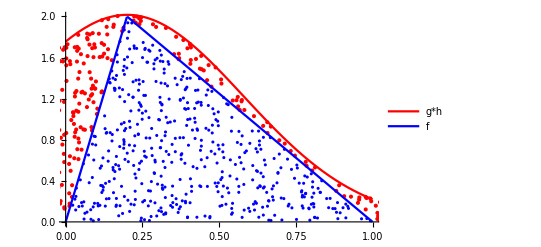

```mathematica
Show[{
ListPlot[smex,PlotStyle->{Red}],
ListPlot[sm,PlotStyle->{Blue}],
Plot[{gpdf[x]*h,fpdf[x]},{x,0,1},PlotLegends->{"g*h","f"},PlotStyle->{Red,Blue}]
},
PlotRange-> {{0,1},{0,2}}
]
```

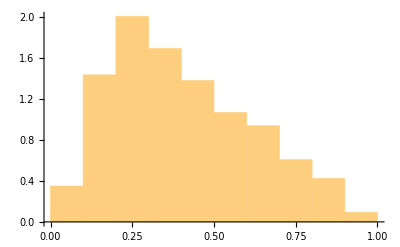

```mathematica
Histogram[sm[[;;,1]],10,"PDF"]
```

```mathematica
Length[sm]/1000
```

501/1000

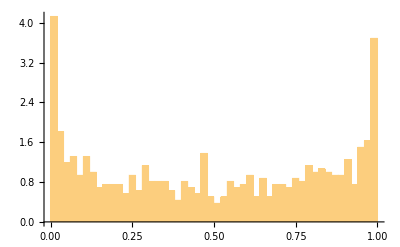

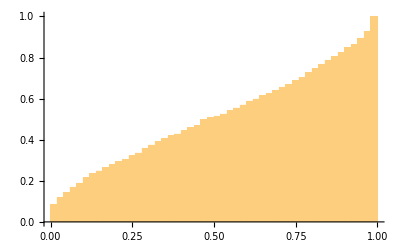

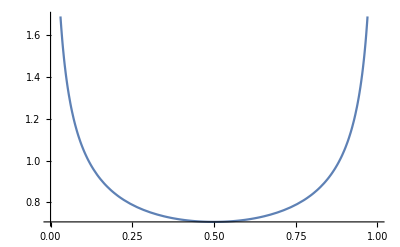

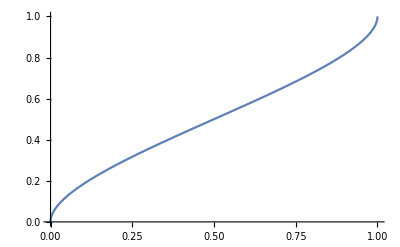

```mathematica
β={1/2,1/2};
lsβ =Sum[β[[n]],{n,1,#}]&/@Range[Length[β]];
xfun={Function[ξ,ξ^2],Function[ξ,2 ξ-ξ^2]};
chpdf={Function[x,1/(2*√x)],Function[x,1/(2*√(1-x))]};
cfpdf[x_]:=Sum[β[[n]]*chpdf[[n]][x],{n,1,2}];
calk[ξ_]:=Position[ξ<#&/@lsβ,True][[1,1]];
ξarray = RandomReal[{0,1},{800}];
xkarray = xfun[[#]][RandomReal[{0,1}]]&/@(calk[#]&/@ξarray);
Histogram[xkarray,40,"PDF"]
Histogram[xkarray,40,"CDF"]
Plot[{cfpdf[x]},{x,0,1}]
Plot[NIntegrate[cfpdf[x],{x,0,r}],{r,0,1}]
```

```mathematica
en[x_,n_]:= NIntegrate[(n*E^(-x*y))/y^n,{y,1,∞}]
```

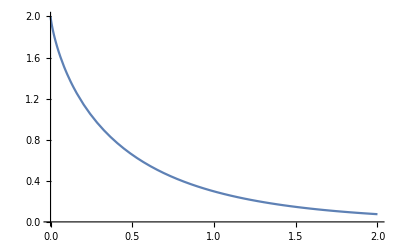

```mathematica
Plot[en[x,2],{x,0,2}]
```

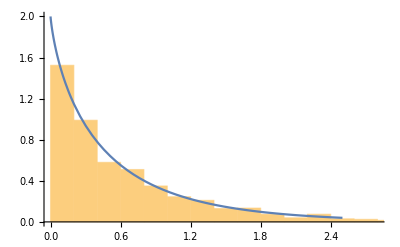

```mathematica
xarray=-RandomReal[{0,1},{1000}]^(1/2)*Log[RandomReal[{0,1},{1000}]];
Show[
{Histogram[xarray,20,"PDF"],
Plot[en[x,2],{x,0,2.5}]}
]
```

```mathematica
Max[xarray]
```

-0.0291447

```mathematica
y-> (1-ξ)^(-1/n)
```

```mathematica
Log[ξ2]/(ξ)^(-1/n)
```

ξ^(1/n) Log[ξ2]